******************************************* EPM Test Setup ******************************************

```mathematica
<<Packages/EPMWorland.m
```

```mathematica
wEPMDir = "/mnt/Computations/Builds/EPM-Serial/";
```

```mathematica
wEPMTestBase=wEPMDir<>"wCheby_";
```

```mathematica
wEPMSetupFile = wEPMTestBase<>"setup.dat";
```

```mathematica
wEPMSetup = Flatten[Import[wEPMSetupFile]];
```

```mathematica
wMaxL = wEPMSetup[[1]]-1;
```

```mathematica
wNr = wEPMSetup[[2]];
```

```mathematica
wMaxN = wEPMSetup[[3]]-1;
```

```mathematica
wEPMFileBase = wEPMTestBase<>"N"<>ToString[wNr];
```

```mathematica
wMaxL=15;
wMaxN=15;
```

```mathematica
epmPrecision =50;
```

***************** Comparison between Mathematic and EPM code ***********************

********************** Comparison of Grid  nodes and Weights ***********************

```mathematica
codeValues = BinaryReadList[wEPMFileBase<>"_grid.data","Real64"];
```

```mathematica
mathValues = EPMWorlandGrid[wMaxN, wMaxL];
```

```mathematica
ListPlot[Abs[codeValues - mathValues], PlotLabel -> "Grid precision", AxesLabel->{"point", "Abs error"}]
```

```mathematica
codeValues = BinaryReadList[wEPMFileBase<>"_weights.data","Real64"];
```

```mathematica
mathValues = EPMWorlandWeights[wMaxN, wMaxL];
```

```mathematica
ListPlot[Abs[codeValues - mathValues], PlotLabel -> "Weights precision", AxesLabel->{"weight", "Abs error"}]
```

********************** Comparison of Polynomial values ***********************

```mathematica
plots ={};
```

```mathematica
For[l=0, l ≤  wMaxL, l++, 
codeValues =Transpose[Partition[BinaryReadList[wEPMFileBase<>"_poly"<>"_L"<>ToString[l]<>".proj", "Real64"],wMaxN+1]];mathValues = EPMWorlandP[wMaxN, wMaxL,l];AppendTo[plots,ListPlot[Abs[codeValues-mathValues], PlotStyle->Red, PlotLabel->"Polynomial errors for l="<>ToString[l], AxesLabel->{"Grid point", "Abs error"}]];]
```

```mathematica
Show[plots[[-1]]]
```

```mathematica
laplL=1;
```

```mathematica
laplacian = SetPrecision[EPMWorlandSpecLaplacian[wMaxN, wMaxL, laplL],epmPrecision];
```

```mathematica
extGNS = N[Table[r^laplL JacobiP[n,-1/2,laplL-1/2, 2 r^2-1], {n,0,wMaxN-1}]/.{r->1.0},epmPrecision];
```

```mathematica
extGSF = N[Table[D[r^laplL JacobiP[n,-1/2,laplL-1/2, 2 r^2-1],r] -1/r r^laplL JacobiP[n,-1/2,laplL-1/2, 2 r^2-1], {n,0,wMaxN-1}]/.{r->1.0},epmPrecision];
```

```mathematica
extHNS =N[r^laplL JacobiP[wMaxN,-1/2,laplL-1/2, 2 r^2-1]/.{r->1.0},epmPrecision];
```

```mathematica
extHSF =N[(D[r^laplL JacobiP[wMaxN,-1/2,laplL-1/2, 2 r^2-1],r] -1/r r^laplL JacobiP[wMaxN,-1/2,laplL-1/2, 2 r^2-1])/.{r->1.0},epmPrecision];
```

```mathematica
extG = -1.0/extHSF extGSF;
```

```mathematica
extG = -1.0/extHNS extGNS;
```

```mathematica
dt = SetPrecision[1,epmPrecision];
c = SetPrecision[1.0,epmPrecision];
```

```mathematica
factor=SetPrecision[dt c,epmPrecision];
```

```mathematica
bLaplacian = SetPrecision[factor (laplacian[[1;;-2,1;;-2]] + Outer[Times,laplacian[[1;;-2,-1]], extG]),epmPrecision];
```

```mathematica
bLaplacian//MatrixForm
```

(-29888. | -14924. | -11157. | -9225. | -7966.875 | -7018.59375 | -6238.8046875 | -5543.484375 | -4895.3759765625 | -4259.8883056640634094947017729282379150390625 | -3624.0209655761727844947017729282379150390625 | -2968.183502197265625 | -2287.4702186584481751197017729282379150390625 | -1568.40789318084716796875 | -809.3994319438934326171875
-59248. | -29624. | -22134. | -18330. | -15820. | -13958.4375 | -12398.203125 | -11033.34375 | -9734.1943359375 | -8484.166259765626818989403545856475830078125 | -7208.573791503908068989403545856475830078125 | -5914.83892822265625 | -4549.151596069337756489403545856475830078125 | -3126.8970012664794921875 | -1604.452049732208251953125
-77760. | -38880. | -29160. | -24120.00000000000363797880709171295166015625 | -20883.33333333333212067373096942901611328125 | -18401.25 | -16396.1875 | -14568.125000000001818989403545856475830078125 | -12895.13671875 | -11217.260742187501818989403545856475830078125 | -9566.3252766927107586525380611419677734375 | -7829.043701171875 | -6051.7814127604187888209708034992218017578125 | -4142.7459081013994364184327423572540283203125 | -2152.0221233367919921875
-90777.60000000000582076609134674072265625 | -45388.800000000002910383045673370361328125 | -34041.5999999999985448084771633148193359375 | -28368.00000000000363797880709171295166015625 | -24514. | -21703.5 | -19294.27499999999781721271574497222900390625 | -17224.35000000000218278728425502777099609375 | -15202.6875 | -13289.78320312500363797880709171295166015625 | -11290.143261718752910383045673370361328125 | -9291.517675781249636202119290828704833984375 | -7138.351257324220568989403545856475830078125 | -4923.6849212646484375 | -2513.561840057373046875
-100352. | -50176. | -37632. | -31360.00000000000363797880709171295166015625 | -27440. | -24228. | -21681. | -19292.74285714285724679939448833465576171875 | -17144.6785714285724679939448833465576171875 | -14927.85937500000363797880709171295166015625 | -12779.30033482142971479333937168121337890625 | -10461.41484375000072759576141834259033203125 | -8120.3903320312520008883439004421234130859375 | -5554.5196533203125 | -2907.621002197267443989403545856475830078125
-106138.41269841269240714609622955322265625 | -53069.206349206346203573048114776611328125 | -39801.9047619047560147009789943695068359375 | -33168.2539682539718342013657093048095703125 | -29022.22222222222262644208967685699462890625 | -26120. | -23283.33333333333212067373096942901611328125 | -20891.61904761904952465556561946868896484375 | -18475.08928571428623399697244167327880859375 | -16224.754464285715584992431104183197021484375 | -13798.27641369047705666162073612213134765625 | -11405.0963541666642413474619388580322265625 | -8760.674045138890505768358707427978515625 | -6070.926242404513686778955161571502685546875 | -3084.944588797434334992431104183197021484375
-109616.761904761908226646482944488525390625 | -54808.3809523809541133232414722442626953125 | -41106.28571428571012802422046661376953125 | -34255.2380952380990493111312389373779296875 | -29973.33333333333212067373096942901611328125 | -26976. | -24728. | -22077.71428571428623399697244167327880859375 | -19736.78571428571376600302755832672119140625 | -17226.1607142857174039818346500396728515625 | -14827.718750000001818989403545856475830078125 | -12155.62784090909190126694738864898681640625 | -9488.507339015153775108046829700469970703125 | -6490.92166785037625231780111789703369140625 | -3428.992095550935118808411061763763427734375
-109226.666666666671517305076122283935546875 | -54613.3333333333357586525380611419677734375 | -40960. | -34133.3333333333357586525380611419677734375 | -29866.66666666666787932626903057098388671875 | -26880. | -24640. | -22880. | -20310. | -17956.25000000000363797880709171295166015625 | -15308.85416666666787932626903057098388671875 | -12730.97159090909190126694738864898681640625 | -9787.496448863637851900421082973480224609375 | -6824.49407688665451132692396640777587890625 | -3453.04518479567559552378952503204345703125
-107057.4097902097855694591999053955078125 | -53528.70489510489278472959995269775390625 | -40146.5286713286695885471999645233154296875 | -33455.4405594405616284348070621490478515625 | -29273.510489510488696396350860595703125 | -26346.15944055944055435247719287872314453125 | -24150.6461538461517193354666233062744140625 | -22425.60000000000218278728425502777099609375 | -21024. | -18428.00000000000363797880709171295166015625 | -15984.9111111111124046146869659423828125 | -13141.206060606060418649576604366302490234375 | -10334.9396464646488311700522899627685546875 | -7077.428491647240662132389843463897705078125 | -3780.656413898601385881192982196807861328125
-100544.247470176880597136914730072021484375 | -50272.1237350884402985684573650360107421875 | -37704.0928013163284049369394779205322265625 | -31420.07733443027609609998762607574462890625 | -27492.5676676264920388348400592803955078125 | -24743.310900863842107355594635009765625 | -22681.3683257918528397567570209503173828125 | -21061.27058823529296205379068851470947265625 | -19744.941176470587379299104213714599609375 | -18648. | -15967.60000000000218278728425502777099609375 | -13391.890909090905552147887647151947021484375 | -10317.172727272729389369487762451171875 | -7253.092220279717366793192923069000244140625 | -3654.956840034965352970175445079803466796875
-92668.973824936678283847868442535400390625 | -46334.4869124683391419239342212677001953125 | -34750.8651843512561754323542118072509765625 | -28959.0543202927146921865642070770263671875 | -25339.17253025612444616854190826416015625 | -22805.25527723050981876440346240997314453125 | -20904.81733746129975770600140094757080078125 | -19411.616099071208736859261989593505859375 | -18198.390092879257281310856342315673828125 | -17187.3684210526334936730563640594482421875 | -16328.000000000001818989403545856475830078125 | -13485.818181818181983544491231441497802734375 | -10713.8181818181838025338947772979736328125 | -7353.365384615384755306877195835113525390625 | -3983.031031468533910810947418212890625
-79815.399494210651027970016002655029296875 | -39907.6997471053255139850080013275146484375 | -29930.77481032898867852054536342620849609375 | -24942.3123419408293557353317737579345703125 | -21824.52329919822295778430998325347900390625 | -19642.0709692784002982079982757568359375 | -18005.23172183853239403106272220611572265625 | -16719.14374170721202972345054149627685546875 | -15674.197257850508322007954120635986328125 | -14803.4085213032594765536487102508544921875 | -14063.238095238097230321727693080902099609375 | -13424. | -10380.66666666666787932626903057098388671875 | -7379.1666666666669698315672576427459716796875 | -3703.537087912089191377162933349609375
-66013.04741294510313309729099273681640625 | -33006.523706472551566548645496368408203125 | -24754.89277985441367491148412227630615234375 | -20629.07731654534654808230698108673095703125 | -18050.44265197717686532996594905853271484375 | -16245.398386779459542594850063323974609375 | -14891.615187881170641048811376094818115234375 | -13827.928388746802738751284778118133544921875 | -12963.682864450127453892491757869720458984375 | -12243.478260869565929169766604900360107421875 | -11631.3043478260879055596888065338134765625 | -11102.60869565217217314057052135467529296875 | -10640. | -7330.76923076923048938624560832977294921875 | -4042.5824175824172925786115229129791259765625
-46508.9217652827719575725495815277099609375 | -23254.46088264138597878627479076385498046875 | -17440.8456619810385745950043201446533203125 | -14534.0380516508666914887726306915283203125 | -12717.283295194507445557974278926849365234375 | -11445.554965675057246698997914791107177734375 | -10491.75871853546777856536209583282470703125 | -9742.347381497222158941440284252166748046875 | -9133.450670153644750826060771942138671875 | -8626.036744033999639214016497135162353515625 | -8194.73490683229829301126301288604736328125 | -7822.2469565217388662858866155147552490234375 | -7496.3200000000006184563972055912017822265625 | -7207.9999999999990905052982270717620849609375 | -3602.5714285714284415007568895816802978515625
-26497.86885628393429215066134929656982421875 | -13248.934428141967146075330674648284912109375 | -9936.7008211064749048091471195220947265625 | -8280.584017588729693670757114887237548828125 | -7245.5110153901377998408861458301544189453125 | -6520.959913851123928907327353954315185546875 | -5977.5465876968637530808337032794952392578125 | -5550.578974289945108466781675815582275390625 | -5203.6677883968231981270946562290191650390625 | -4914.5751334858896370860747992992401123046875 | -4668.84637681159438216127455234527587890625 | -4456.626086956521248794160783290863037109375 | -4270.9333333333333939663134515285491943359375 | -4106.666666666666060336865484714508056640625 | -3960.00000000000045474735088646411895751953125)

```mathematica
expEig=Eigenvalues[MatrixExp[(1/3)3 10^-3 bLaplacian]]
```

{0.98001173925618181102669435459829855017066567562855,0.94206640247116623276574235474629859855083971761981,0.8878967021503870751660155560739341434833887777969,0.82048650884155180769301704581269532384964668049947,0.74337517756195732932381138754912250737473552533168,0.66034689983192158523339706081707052554644924433694,0.57513151434444934344071504918109571413978763594655,0.49153390274711207643703802171733629082545033966057,0.4169362118041654630691856644308793762402278457424,0.33892622128848771576791418147136368240811606629466,0.22322238940553775673536413015754951768743061524851,0.089850299957742518918314492188711806134556813790533,0.0081002810756767177949671626249255116607439484565023,2.2529385628508324244852628283014535818209670430003×10^-7,4.2577267600339080508720139577485166869020581832436×10^-67}

```mathematica
pcEig=Reverse@Sort@Eigenvalues[Inverse[(3IdentityMatrix[wMaxN] - 3 10^-3 1/2 bLaplacian)].(3 IdentityMatrix[wMaxN] + 3 10^-3 1/2 bLaplacian)]
```

{0.980011067003703895089412048846462764649283558,0.942049706779987096338344919433865621035430047,0.887772073712419414443658995011151201674991817,0.819953947716017771991720512309714480189877944,0.741739703153364649786008412470467188903837327,0.656321574564446250851509101583800476699519331,0.566688109982958494241872509384848742781312397,0.475892569503281807513562084442422800653400074,0.391390474567901623424931750361949357806849587,0.297869974381588235389269942070137120753312599,0.14299210000047706708406472943659806944619628,-0.0928903682920843851363693402678522958639756106,-0.413133185843485104784020779488574047305047746,-0.768864422793541506125681144520842682684307394,-0.98586975564864852998666375056771249032165945}

```mathematica
lhs = Inverse[(10^4 IdentityMatrix[wMaxN] - 10 1/2 bLaplacian)];
```

```mathematica
rhs =(10^4 IdentityMatrix[wMaxN] +10 1/2 bLaplacian);
```

```mathematica
Reverse@Sort@Eigenvalues[lhs . rhs]//MatrixForm
```

(0.980011067003703895089412048846462764649283558
0.942049706779987096338344919433865621035430047
0.887772073712419414443658995011151201674991817
0.819953947716017771991720512309714480189877944
0.741739703153364649786008412470467188903837327
0.656321574564446250851509101583800476699519331
0.566688109982958494241872509384848742781312397
0.475892569503281807513562084442422800653400074
0.391390474567901623424931750361949357806849587
0.297869974381588235389269942070137120753312599
0.14299210000047706708406472943659806944619628
-0.0928903682920843851363693402678522958639756106
-0.413133185843485104784020779488574047305047746
-0.768864422793541506125681144520842682684307394
-0.98586975564864852998666375056771249032165945)

```mathematica
Eigenvalues@MatrixExp[10 10^-4 bLaplacian]
```

{0.98001173925618181102669435459829855017066567562855,0.94206640247116623276574235474629859855083971761981,0.8878967021503870751660155560739341434833887777969,0.82048650884155180769301704581269532384964668049947,0.74337517756195732932381138754912250737473552533168,0.66034689983192158523339706081707052554644924433694,0.57513151434444934344071504918109571413978763594655,0.49153390274711207643703802171733629082545033966057,0.4169362118041654630691856644308793762402278457424,0.33892622128848771576791418147136368240811606629466,0.22322238940553775673536413015754951768743061524851,0.089850299957742518918314492188711806134556813790533,0.0081002810756767177949671626249255116607439484565023,2.2529385628508324244852628283014535818209670430003×10^-7,4.2577267600339080508720139577485166869020581832436×10^-67}

```mathematica
Eigenvalues[MatrixExp[200 10^-3 bLaplacian]]//MatrixForm
```

(0.01763013348229611338818579679804407270466979340516
6.5509322590338293497742580436557523825062804048411×10^-6
4.70423040573821781844811276084883625860809055478×10^-11
6.520619815865974777906790019873150084040964312146×10^-18
1.7442593051909151299917275471840977646512673671237×10^-26
9.0038583692795254624831741378733599915138910009206×10^-37
8.983241707023651421190229528229732630408249664075×10^-49
2.045010728057403216450801906025353740729509692194×10^-62
-2.4489589743088923537581608670898250902537298336324×10^-72
-1.8061253270843945935204109862644896318007223414419×10^-75
5.3252810092166878886053273976453629064700804867815×10^-76
-1.6705638887772726175507932976919858101830462554395×10^-76+3.2576586689881983928863440798796859458253646767422×10^-76 ⅈ
-1.6705638887772726175507932976919858101830462554395×10^-76-3.2576586689881983928863440798796859458253646767422×10^-76 ⅈ
1.1354606052985678285860545856164661709241895405821×10^-76
8.9563540193447466408552700172124635830488825357935×10^-79)

```mathematica
SetPrecision[Abs[100 (expEig - pcEig)/expEig] ,3]
```

{0.0000686,0.00177,0.014,0.0649,0.22,0.61,1.47,3.18,6.13,12.1,35.9,203.,5200.,3.41×10^8,2.32×10^68}

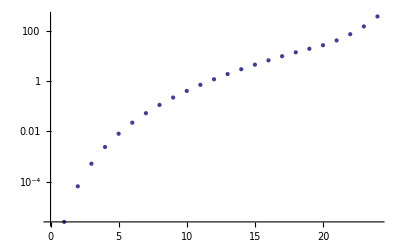

```mathematica
ListLogPlot[Abs[100 (expEig - pcEig)/expEig][[1;;-8]]]
```

```mathematica
1.0/Eigenvalues[(3IdentityMatrix[wMaxN] -  3 10^-3 1/2 bLaplacian)]
```

{0.000664996,0.0118506,0.0352102,0.0643981,0.0942074,0.121094,0.143412,0.16063,0.174348,0.188012,0.202835,0.218855,0.23611,0.254724,0.275266}

```mathematica
Min[Eigenvalues[bLaplacian]]
```

-281.081

```mathematica
Max[Eigenvalues[bLaplacian]]
```

-0.0201907

```mathematica
i0 = IdentityMatrix[wMaxN];
i0[[1,1]] = 0;
```

```mathematica
exp0=SetPrecision[Sum[MatrixPower[factor laplacian,i]/(i !), {i,0,16}],epmPrecision];
```

```mathematica
m00 = SetPrecision[exp0[[1;;-2,1;;-2]] + Outer[Times,exp0[[1;;-2,-1]], extG],epmPrecision];
```

```mathematica
m0=SetPrecision[Sum[MatrixPower[bLaplacian,i]/(i !), {i,0,16}],epmPrecision];
```

```mathematica
exp1=SetPrecision[Sum[MatrixPower[factor laplacian,i-1]/(i !), {i,1,16}],epmPrecision];
```

```mathematica
m11 = SetPrecision[exp1[[1;;-2,1;;-2]] + Outer[Times,exp1[[1;;-2,-1]], extG],epmPrecision];
```

```mathematica
m1=SetPrecision[Sum[MatrixPower[bLaplacian,i-1]/(i !), {i,1,16}],epmPrecision];
```

```mathematica
m10=SetPrecision[Sum[(i0. MatrixPower[i0.bLaplacian,i-1])/(i !), {i,1,16}],epmPrecision];
```

```mathematica
exp2=SetPrecision[Sum[MatrixPower[factor laplacian,i-2]/(i !), {i,2,16}],epmPrecision];
```

```mathematica
m22 = SetPrecision[exp2[[1;;-2,1;;-2]] + Outer[Times,exp2[[1;;-2,-1]], extG],epmPrecision];
```

```mathematica
m2=SetPrecision[Sum[MatrixPower[bLaplacian,i-2]/(i !), {i,2,16}],epmPrecision];
```

```mathematica
m20=SetPrecision[Sum[(i0. MatrixPower[i0.bLaplacian,i-2])/(i !), {i,2,16}],epmPrecision];
```

```mathematica
Eigenvalues[bLaplacian]
```

```mathematica
Eigenvalues[m0]
```

```mathematica
Eigenvalues[m00]
```

```mathematica
Eigenvalues[m1]
```

```mathematica
Eigenvalues[m11]
```

```mathematica
Eigenvalues[m2]
```

```mathematica
Eigenvalues[m22]
```